```mathematica
SetDirectory[NotebookDirectory[]];
Needs["CCompilerDriver`"];
```

```mathematica
LibraryUnload[aDescLib];
SetDirectory[NotebookDirectory[]];
nPrms=30;
(* We already know the number of parameters at compile time *)
compileFlag=ToString@StringForm["MAXDIM=``",nPrms];
aDescLib=CreateLibrary[{"analytic-descent.c"},"aDescLib","Debug"->False,"Defines"->compileFlag];
computeGradientLOCAL=LibraryFunctionLoad[aDescLib,"compute_gradient",{{Real,1},Integer},{Real,1}];
computeVarianceLOCAL=LibraryFunctionLoad[aDescLib,"compute_variance",{{Real,1},Integer},{Real,1}];
computeGradient[dat_,ths_,nPrms_]:=With[
{temp=computeGradientLOCAL[Join[dat,ths],nPrms]},
Return[{temp[[1]],temp[[2;;]]}]
];
computeVariance[measurementVariances_,ths_,nPrms_]:=With[
{temp=computeVarianceLOCAL[Join[measurementVariances,ths],nPrms]},
Return[temp]
];
```

LibraryUnload::strfile: String or valid File object is expected at position 1 in LibraryUnload[aDescLib]. A valid File has the form File[string].

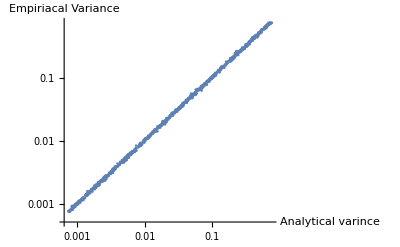

```mathematica
figData=Table[
(* generate random displacement vector *)
v=RandomReal[10^RandomReal[{-3,-1}]{-1,1},nPrms];

(* generate random single-shot variances of the coefficients *)
var=10^RandomReal[{-4,-1}];
(* all coefficient have the same single-shot variances *)
measurementVariances=ConstantArray[var,1+2*nPrms+nPrms*nPrms];
(* generate analytic descent coefficients randomly *)
data=RandomReal[{-1,1},1+2*nPrms+nPrms*nPrms];

(* Call the efficient C code to compute the variance propagation factors *)
cals=computeVariance[measurementVariances,v,nPrms];
(* Call the efficient C code to compute the gradient vector *)
gradRef=computeGradient[data,v,nPrms][[2]];

(* generate Gaussion noise and determine gradient many times *)
estimated=Mean@Table[
noise=RandomVariate[NormalDistribution[0,Sqrt[var]],1+2*nPrms+nPrms*nPrms];
noiseData=data+noise;
grad=computeGradient[noiseData,v,nPrms][[2]];
(* compute mean of the average distance squared *)
Norm[grad-gradRef]^2
,50];

(* compute analytical formula *)
analyitical=Total[cals];

{estimated,analyitical}
,1000];

ListPlot[figData,ScalingFunctions->{"Log","Log"},AxesLabel->{"Analytical varince","Empiriacal Variance"}]
```